## 733406627500 - Succesful Concatination. Reduce Further

### Observations

Concatinated but could be reduced further. It also contains { }

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
733406627500:{"AA"->"AB","AB"->"BA","B"->"AAAAA"}
```

Syntax::tsntxi: "733406627500:{AA->AB,AB->BA,B->AAAAA}" is incomplete; more input is needed.

```mathematica
rs01=FromReducedRankIndex[733406627500]
```

<|Index→733406627500,QCode→32342342432423333,RuleSet→{AA→AB,AB→BA,B→AAAAA}|>

```mathematica
rs01[["RuleSet"]]
```

{AA→AB,AB→BA,B→AAAAA}




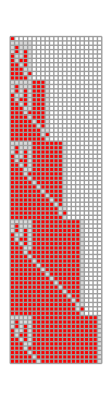
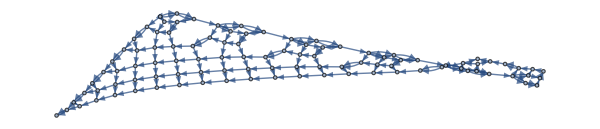
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "B",500,
 SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
sss01[["Net"]]//Short
```

{1→2,1→2,1→3,1→3,2→4,2→4,4→5,«972»,497→498,437→498,498→499,438→499,499→500,439→500}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1,1,2,2,7},{2,2},{2,4},{1,6},{1,1},{1,13},{1,13},{1,1},{12,13},{1,1,2,2,7},{2,2},{2,4},{1,11},{1,1},{1,18},{1,18},{1,1},{1,17},{1,17},{1,17},{1,17},{1,1},{16,17},{1,1,2,2,7},{2,2},{2,4},{1,15},{1,1},{1,22},{1,22},{1,1},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,1},{20,21},{1,1,2,2,7},{2,2},{2,4},{1,19},{1,1},{1,26},{1,26},{1,1},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,1},{24,25},{1,1,2,2,7},{2,2},{2,4},{1,23},{1,1},{1,30},{1,30},{1,1},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,1},{28,29},{1,1,2,2,7},{2,2},{2,4},{1,27},{1,1},{1,34},{1,34},{1,1},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,1},{32,33},{1,1,2,2,7},{2,2},{2,4},{1,31},{1,1},{1,38},{1,38},{1,1},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,1},{36,37},{1,1,2,2,7},{2,2},{2,4},{1,35},{1,1},{1,42},{1,42},{1,1},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,1},{40,41},{1,1,2,2,7},{2,2},{2,4},{1,39},{1,1},{1,46},{1,46},{1,1},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,45},{1,1},{44,45},{1,1,2,2,7},{2,2},{2,4},{1,43},{1,1},{1,50},{1,50},{1,1},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,49},{1,1},{48,49},{1,1,2,2,7},{2,2},{2,4},{1,47},{1,1},{1,54},{1,54},{1,1},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,53},{1,1},{52,53},{1,1,2,2,7},{2,2},{2,4},{1,51},{1,1},{1,58},{1,58},{1,1},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,57},{1,1},{56,57},{1,1,2,2,7},{2,2},{2,4},{1,55},{1,1},{1,62},{1,62},{1,1},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,61},{1,1},{},{1,1,2,2,7},{2,2},{2,4},{1},{1,1},{1},{1},{1,1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
rslo1=ReduceSetList[nds01]
```

{{1,1,2,2,7},€_(n$1⊨1)^2[{2,2+2 (-1+n$1)}],{1,6},{1,1},€^2[{1,13}],{1,1},€_(n$3⊨1)^12[{4 (2+n$3),9+4 n$3},{1,1,2,2,7},€_(n$1⊨1)^2[{2,2+2 (-1+n$1)}],{1,7+4 n$3},€_(n$2⊨1)^3[€^(2 n$2 (-1+2 n$3)-2 (-3+4 n$3))[{1,-n$2+4 (4+n$3)}],{1,1}]],{},{1,1,2,2,7},€_(n$1⊨1)^2[{2,2+2 (-1+n$1)}],{1},€_(n$2⊨1)^2[€^(-94+48 n$2)[{1}],{1,1}],€^50[{1}]}